1-4/z

Abs[1-5/z]

1-5/z

Abs[1-6/z]

1-6/z

Abs[1-7/z]

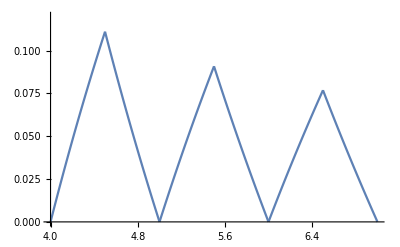

```mathematica
f[z_]=1 - 4/z
g[z_]=Abs[1-5/z]
f2[z_]=1 - 5/z
g2[z_]=Abs[1-6/z]
f3[z_]=1 - 6/z
g3[z_]=Abs[1-7/z]
Show[
Plot[f[z],{z,4,4.5}],
Plot[g[z],{z,4.5,5}],
Plot[f2[z],{z,5,5.5}],
Plot[g2[z],{z,5.5,6}],
Plot[f3[z],{z,6,6.5}],
Plot[g3[z],{z,6.5,7}],
PlotRange->{{4,7},{0,0.12}}
]
```